```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
delta = 0.5;
K = 20;
H=-px[T]*x[T]-K*y[T]*( (1-delta)*py[T] + (px[T]-py[T])*(py[T]+1)*(x[T]+1)  );
D[H,px[T]]
```

-x[T]-20 (1+py[T]) (1+x[T]) y[T]

```mathematica
system1=NDSolveProblem[{{px'[T]==D[H,x[T]],x'[T]==-D[H,px[T]],py'[T]==D[H,y[T]],y'[T]==-D[H,py[T]]},{px[0]==-0.00001,x[0]==-delta,py[0]==0,y[0]==delta/(K*(1-delta))},{px[T],x[T],py[T],y[T]},{T,0.,5.},{},{ -px[T]*x[T]-K*y[T]*( (1-delta)*py[T] + (px[T]-py[T])*(py[T]+1)*(x[T]+1)  )},{}}];
eqs={system1["System"],system1["InitialConditions"]};
vars=system1["DependentVariables"];
H=system1["Invariants"];
time={T,0.,5.};
step=1./100.;
```

```mathematica
(* sol1=NDSolve[eqs,vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{x[T],y[T]}},StartingStepSize->step,MaxSteps->Infinity] *)
sol1=NDSolve[eqs,vars,time,Method->{"ImplicitRungeKutta","DifferenceOrder"->2,"Coefficients"->ImplicitRungeKuttaGaussCoefficients[4,50]},StartingStepSize->step,MaxSteps->Infinity]
```

NDSolve::csymb: Value of Coefficients -> ImplicitRungeKuttaGaussCoefficients[4,50] of the method ImplicitRungeKutta is not a symbol.

NDSolve::initf: The initialization of the method NDSolve`ImplicitRungeKutta failed.

{{px[T]→InterpolatingFunction[…][T],x[T]→InterpolatingFunction[…][T],py[T]→InterpolatingFunction[…][T],y[T]→InterpolatingFunction[…][T]}}

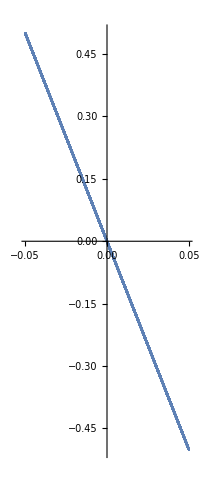

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

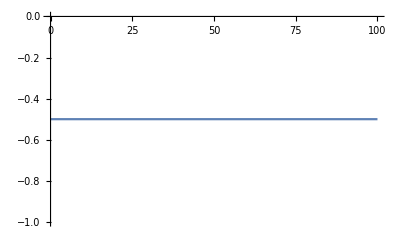

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

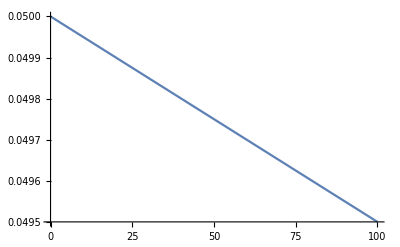

```mathematica
ParametricPlot[Evaluate[{y[T],x[T]}/.First[sol]],Evaluate[time]]
Plot[Evaluate[x[T]/.First[sol1]],Evaluate[time]]
Plot[Evaluate[y[T]/.First[sol1]],Evaluate[time]]
```

```mathematica
system=GetNDSolveProblem["HarmonicOscillator"]
eqs={system["System"],system["InitialConditions"]};
vars=system["DependentVariables"];
H=system["Invariants"];
time={T,0,100};
step=1/25;
```

NDSolveProblem[{{Y_1'[T]==Y_2[T],Y_2'[T]==-Y_1[T]},{Y_1[0]==1,Y_2[0]==0},{Y_1[T],Y_2[T]},{T,0,10},{},{1/2 (Y_1[T]^2+Y_2[T]^2)},{}}]

```mathematica
NDSolveProblem[{{Subscript[Y, 1]'[T]==Subscript[Y, 2][T],Subscript[Y, 2]'[T]==-Subscript[Y, 1][T]},{Subscript[Y, 1][0]==1,Subscript[Y, 2][0]==0},{Subscript[Y, 1][T],Subscript[Y, 2][T]},{T,0,10},{},{1/2 ((Subscript[Y, 1][T])^2+(Subscript[Y, 2][T])^2)},{}}]
sol=NDSolve[eqs,vars,time,Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{Subscript[Y,1][T]}},StartingStepSize->step,MaxSteps->Infinity];
```

NDSolveProblem[{{Y_1'[T]==Y_2[T],Y_2'[T]==-Y_1[T]},{Y_1[0]==1,Y_2[0]==0},{Y_1[T],Y_2[T]},{T,0,10},{},{1/2 (Y_1[T]^2+Y_2[T]^2)},{}}]

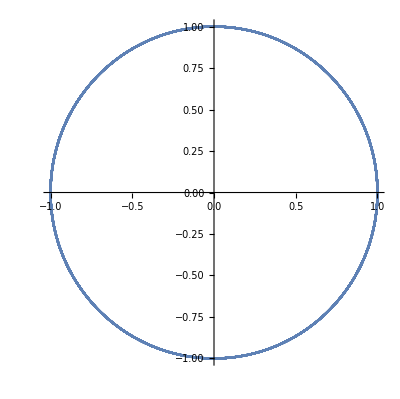

```mathematica
ParametricPlot[Evaluate[vars/.First[sol]],Evaluate[time]]
```